```mathematica
PermulateMultiply[Srtst_,list1_,list2_]:=Srtst/.list1/.list2;
PrmltMltplExch[llset_]:=Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}];
PrmltMltplExchPst[llset_]:={Exch[{llset[[1]],PermulateMultiply[llset[[1]],llset[[2]],llset[[3]]]}],llset[[4]],llset[[5]]};
Exch[list_]:=Module[{len=Length[list[[1]]],per={}},For[Exchi=1,Exchi≤Length[list[[1]]],Exchi++,If[list[[1,Exchi]]≠ list[[2,Exchi]],per=per∪{list[[1,Exchi]]->list[[2,Exchi]]}]];
per
]
```

```mathematica
S1={11->17,17->19,19->13,13->11,14->18,18->16,16->12,12->14,31->61,61->43,43->53,53->31,33->63,63->41,41->51,51->33,32->62,62->42,42->52,52->32};
S2={34->64,64->46,46->56,56->34,35->65,65->45,45->55,55->35,36->66,66->44,44->54,54->36};
S3={21->27,27->29,29->23,23->21,24->28,28->26,26->22,22->24,37->67,67->49,49->59,59->37,39->69,69->47,47->57,57->39,38->68,68->48,48->58,58->38};
S4={51->57,57->59,59->53,53->51,54->58,58->56,56->52,52->54,11->31,31->27,27->47,47->11,17->37,37->21,21->41,41->17,14->34,34->24,24->44,44->14};
S5={12->32,32->28,28->48,48->12,18->38,38->22,22->42,42->18,15->35,35->25,25->45,45->15};
S6={61->67,67->69,69->63,63->61,64->68,68->66,66->62,62->64,13->33,33->29,29->49,49->13,19->39,39->23,23->43,43->19,16->36,36->26,26->46,46->16};
S7={31->33,33->39,39->37,37->31,32->36,36->38,38->34,34->32,17->61,61->29,29->57,57->17,19->67,67->27,27->51,51->19,18->64,64->28,28->54,54->18};
S8={14->62,62->26,26->58,58->14,16->68,68->24,24->52,52->16,15->65,65->25,25->55,55->15};
S9={41->43,43->49,49->47,47->41,42->46,46->48,48->44,44->42,11->63,63->23,23->59,59->11,13->69,69->21,21->53,53->13,12->66,66->22,22->56,56->12};
StartSet={31,32,33,34,35,36,37,38,39,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,11,12,13,14,15,16,17,18,19,21,22,23,24,25,26,27,28,29};
IS1=Exch[{StartSet,StartSet/.S1/.S1/.S1}];
IS2=Exch[{StartSet,StartSet/.S2/.S2/.S2}];
IS3=Exch[{StartSet,StartSet/.S3/.S3/.S3}];
IS4=Exch[{StartSet,StartSet/.S4/.S4/.S4}];
IS5=Exch[{StartSet,StartSet/.S5/.S5/.S5}];
IS6=Exch[{StartSet,StartSet/.S6/.S6/.S6}];
IS7=Exch[{StartSet,StartSet/.S7/.S7/.S7}];
IS8=Exch[{StartSet,StartSet/.S8/.S8/.S8}];
IS9=Exch[{StartSet,StartSet/.S9/.S9/.S9}];
```

```mathematica
Sl1={{11->17,"S1"},{17->19,"S1"},{19->13,"S1"},{13->11,"S1"},{14->18,"S1"},{18->16,"S1"},{16->12,"S1"},{12->14,"S1"},{31->61,"S1"},{61->43,"S1"},{43->53,"S1"},{53->31,"S1"},{33->63,"S1"},{63->41,"S1"},{41->51,"S1"},{51->33,"S1"},{32->62,"S1"},{62->42,"S1"},{42->52,"S1"},{52->32,"S1"}};
Sl2={{34->64,"S2"},{64->46,"S2"},{46->56,"S2"},{56->34,"S2"},{35->65,"S2"},{65->45,"S2"},{45->55,"S2"},{55->35,"S2"},{36->66,"S2"},{66->44,"S2"},{44->54,"S2"},{54->36,"S2"}};
Sl3={{21->27,"S3"},{27->29,"S3"},{29->23,"S3"},{23->21,"S3"},{24->28,"S3"},{28->26,"S3"},{26->22,"S3"},{22->24,"S3"},{37->67,"S3"},{67->49,"S3"},{49->59,"S3"},{59->37,"S3"},{39->69,"S3"},{69->47,"S3"},{47->57,"S3"},{57->39,"S3"},{38->68,"S3"},{68->48,"S3"},{48->58,"S3"},{58->38,"S3"}};
Sl4={{51->57,"S4"},{57->59,"S4"},{59->53,"S4"},{53->51,"S4"},{54->58,"S4"},{58->56,"S4"},{56->52,"S4"},{52->54,"S4"},{11->31,"S4"},{31->27,"S4"},{27->47,"S4"},{47->11,"S4"},{17->37,"S4"},{37->21,"S4"},{21->41,"S4"},{41->17,"S4"},{14->34,"S4"},{34->24,"S4"},{24->44,"S4"},{44->14,"S4"}};
Sl5={{12->32,"S5"},{32->28,"S5"},{28->48,"S5"},{48->12,"S5"},{18->38,"S5"},{38->22,"S5"},{22->42,"S5"},{42->18,"S5"},{15->35,"S5"},{35->25,"S5"},{25->45,"S5"},{45->15,"S5"}};
Sl6={{61->67,"S6"},{67->69,"S6"},{69->63,"S6"},{63->61,"S6"},{64->68,"S6"},{68->66,"S6"},{66->62,"S6"},{62->64,"S6"},{13->33,"S6"},{33->29,"S6"},{29->49,"S6"},{49->13,"S6"},{19->39,"S6"},{39->23,"S6"},{23->43,"S6"},{43->19,"S6"},{16->36,"S6"},{36->26,"S6"},{26->46,"S6"},{46->16,"S6"}};
Sl7={{31->33,"S7"},{33->39,"S7"},{39->37,"S7"},{37->31,"S7"},{32->36,"S7"},{36->38,"S7"},{38->34,"S7"},{34->32,"S7"},{17->61,"S7"},{61->29,"S7"},{29->57,"S7"},{57->17,"S7"},{19->67,"S7"},{67->27,"S7"},{27->51,"S7"},{51->19,"S7"},{18->64,"S7"},{64->28,"S7"},{28->54,"S7"},{54->18,"S7"}};
Sl8={{14->62,"S8"},{62->26,"S8"},{26->58,"S8"},{58->14,"S8"},{16->68,"S8"},{68->24,"S8"},{24->52,"S8"},{52->16,"S8"},{15->65,"S8"},{65->25,"S8"},{25->55,"S8"},{55->15,"S8"}};
Sl9={{41->43,"S9"},{43->49,"S9"},{49->47,"S9"},{47->41,"S9"},{42->46,"S9"},{46->48,"S9"},{48->44,"S9"},{44->42,"S9"},{11->63,"S9"},{63->23,"S9"},{23->59,"S9"},{59->11,"S9"},{13->69,"S9"},{69->21,"S9"},{21->53,"S9"},{53->13,"S9"},{12->66,"S9"},{66->22,"S9"},{22->56,"S9"},{56->12,"S9"}};
```

```mathematica
S1, S2,S3,S5,S6,S7,S8,S7,S9

S2,S3,S5,S6,S7,S8(*保持11,41,53不动的完备系,12到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Sl5∪Sl6∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True]
```

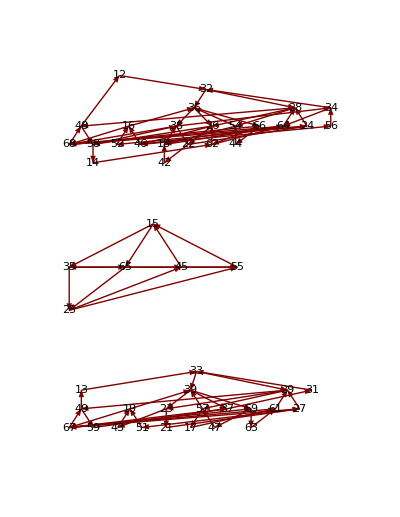

```mathematica
S2,S3,S5,S6,S7,S8(*保持11,41,53不动的完备系,12到任意位置*)

S2,S3,S6,S7,S8(*保持11,41,53,12,42不动的完备系,13到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Sl6∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True]
```

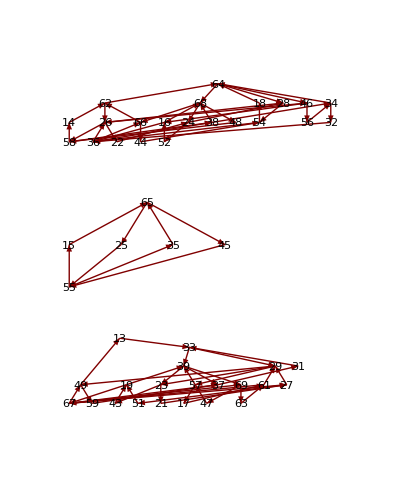

```mathematica
S2,S3,S6,S7,S8(*保持11,41,53,12,42不动的完备系,13到任意位置*)

S2,S3,S7,S8(*保持11,41,53,12,42,13,63,43不动的完备系,14到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪Sl8,VertexLabeling->True,DirectedEdges-> True]
```

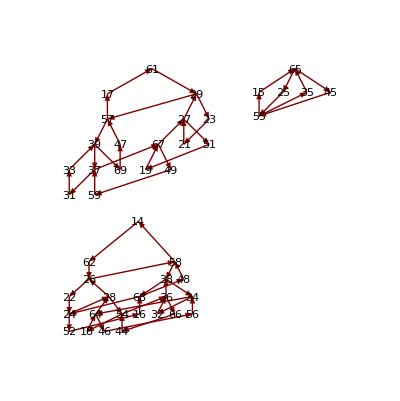

```mathematica
T1=Exch[{StartSet,StartSet/.S8/.S3/.IS8}](*S8^-1 S3 S8*)
```

{16→48,21→27,22→68,23→21,26→38,27→29,28→62,29→23,37→67,38→16,39→69,47→57,48→26,49→59,57→39,59→37,62→22,67→49,68→28,69→47}

```mathematica
Table[{T1[[i]],"T1"},{i,Length[T1]}]//InputForm
```

{{16 -> 48, "T1"}, {21 -> 27, "T1"}, {22 -> 68, "T1"}, {23 -> 21, "T1"}, {26 -> 38, "T1"}, {27 -> 29, "T1"}, {28 -> 62, "T1"}, {29 -> 23, "T1"}, 
 {37 -> 67, "T1"}, {38 -> 16, "T1"}, {39 -> 69, "T1"}, {47 -> 57, "T1"}, {48 -> 26, "T1"}, {49 -> 59, "T1"}, {57 -> 39, "T1"}, {59 -> 37, "T1"}, 
 {62 -> 22, "T1"}, {67 -> 49, "T1"}, {68 -> 28, "T1"}, {69 -> 47, "T1"}}

```mathematica
Tl1={{16->48,"T1"},{21->27,"T1"},{22->68,"T1"},{23->21,"T1"},{26->38,"T1"},{27->29,"T1"},{28->62,"T1"},{29->23,"T1"},{37->67,"T1"},{38->16,"T1"},{39->69,"T1"},{47->57,"T1"},{48->26,"T1"},{49->59,"T1"},{57->39,"T1"},{59->37,"T1"},{62->22,"T1"},{67->49,"T1"},{68->28,"T1"},{69->47,"T1"}};
```

```mathematica
IT1=Exch[{StartSet,StartSet/.T1/.T1/.T1}];
```

```mathematica
S2,S3,S7,S8(*保持11,41,53,12,42,13,63,43不动的完备系,14到任意位置*)

S2,S3,S7,T1=S8^-1 S3 S8(*保持11,41,53,12,42,13,63,43,14,54不动的完备系,16到任意位置*)
```

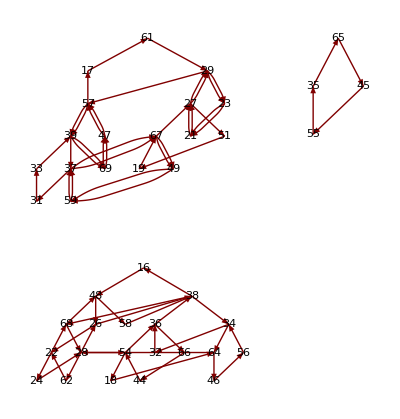

```mathematica
TreePlot[Sl2∪Sl3∪Sl7∪Tl1,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
S2,S3,S7,T1=S8^-1 S3 S8(*保持11,41,53,12,42,13,63,43,14,54不动的完备系,16到任意位置*)

S2,S3,S7(*保持11,41,53,12,42,13,63,43,14,54,16,62不动的完备系,17到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Sl7,VertexLabeling->True,DirectedEdges-> True]
```

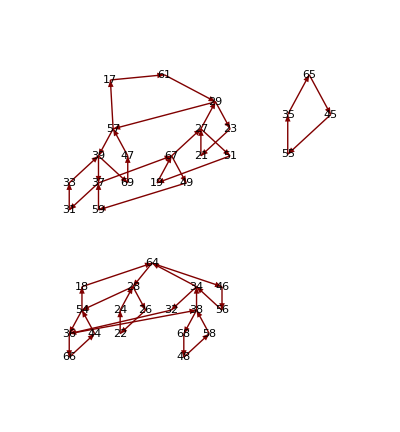

```mathematica
T2=Exch[{StartSet,StartSet/.S7/.S3/.IS7}](*S7^-1 S3 S7*)
T3=Exch[{StartSet,StartSet/.S5/.S3/.IS5}](*S5^-1 S3 S5*)
```

{19→49,21→67,22→24,23→21,24→64,26→22,29→33,33→69,36→68,39→19,47→29,48→58,49→59,58→36,59→39,61→23,64→26,67→61,68→48,69→47}

{18→68,21→27,23→21,24→32,26→38,27→29,28→58,29→23,32→26,37→67,38→24,39→69,47→57,49→59,57→39,58→18,59→37,67→49,68→28,69→47}

```mathematica
IT2=Exch[{StartSet,StartSet/.T2/.T2/.T2}];
```

```mathematica
IT3=Exch[{StartSet,StartSet/.T3/.T3/.T3}];
```

```mathematica
Table[{T3[[i]],"T3"},{i,Length[T3]}]//InputForm
```

{{18 -> 68, "T3"}, {21 -> 27, "T3"}, {23 -> 21, "T3"}, {24 -> 32, "T3"}, {26 -> 38, "T3"}, {27 -> 29, "T3"}, {28 -> 58, "T3"}, {29 -> 23, "T3"}, 
 {32 -> 26, "T3"}, {37 -> 67, "T3"}, {38 -> 24, "T3"}, {39 -> 69, "T3"}, {47 -> 57, "T3"}, {49 -> 59, "T3"}, {57 -> 39, "T3"}, {58 -> 18, "T3"}, 
 {59 -> 37, "T3"}, {67 -> 49, "T3"}, {68 -> 28, "T3"}, {69 -> 47, "T3"}}

```mathematica
Tl2={{19->49,"T2"},{21->67,"T2"},{22->24,"T2"},{23->21,"T2"},{24->64,"T2"},{26->22,"T2"},{29->33,"T2"},{33->69,"T2"},{36->68,"T2"},{39->19,"T2"},{47->29,"T2"},{48->58,"T2"},{49->59,"T2"},{58->36,"T2"},{59->39,"T2"},{61->23,"T2"},{64->26,"T2"},{67->61,"T2"},{68->48,"T2"},{69->47,"T2"}};
Tl3={{18->68,"T3"},{21->27,"T3"},{23->21,"T3"},{24->32,"T3"},{26->38,"T3"},{27->29,"T3"},{28->58,"T3"},{29->23,"T3"},{32->26,"T3"},{37->67,"T3"},{38->24,"T3"},{39->69,"T3"},{47->57,"T3"},{49->59,"T3"},{57->39,"T3"},{58->18,"T3"},{59->37,"T3"},{67->49,"T3"},{68->28,"T3"},{69->47,"T3"}};
```

```mathematica
S2,S3,S7(*保持11,41,53,12,42,13,63,43,14,54,16,62不动的完备系,17到任意位置*)

S2,S3,T2=S7^-1 S3 S7,T3=S5^-1 S3 S5(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51不动的完备系,18到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl2∪Tl3,VertexLabeling->True,DirectedEdges-> True]
```

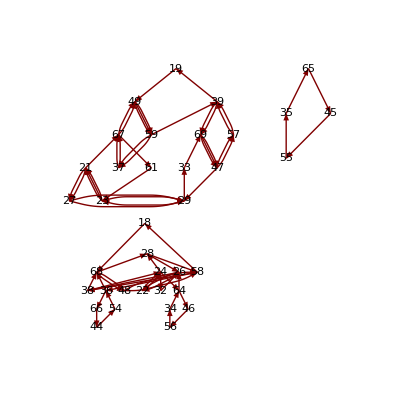

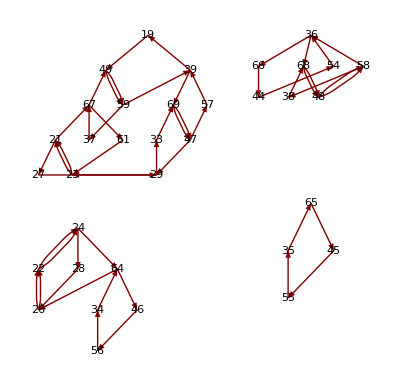

```mathematica
TreePlot[Sl2∪Sl3∪Tl2,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T4=Exch[{StartSet,StartSet/.S5/.S3/.IS5/.S3/.S3/.S5/.S3/.IS5}](*S5^-1 S3 S5 S3^2 S5^-1 S3 S5*)
```

{22→58,24→26,26→48,48→24,58→68,68→22}

```mathematica
IT4=Exch[{StartSet,StartSet/.T4/.T4}];
```

```mathematica
Table[{T4[[i]],"T4"},{i,Length[T4]}]//InputForm
```

{{22 -> 58, "T4"}, {24 -> 26, "T4"}, {26 -> 48, "T4"}, {48 -> 24, "T4"}, {58 -> 68, "T4"}, {68 -> 22, "T4"}}

```mathematica
Tl4={{22->58,"T4"},{24->26,"T4"},{26->48,"T4"},{48->24,"T4"},{58->68,"T4"},{68->22,"T4"}};
```

```mathematica
S2,S3,T2=S7^-1 S3 S7,T3=S5^-1 S3 S5(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51不动的完备系,18到任意位置*)

S2,S3,T2=S7^-1 S3 S7,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32不动的完备系,19到任意位置*)
```

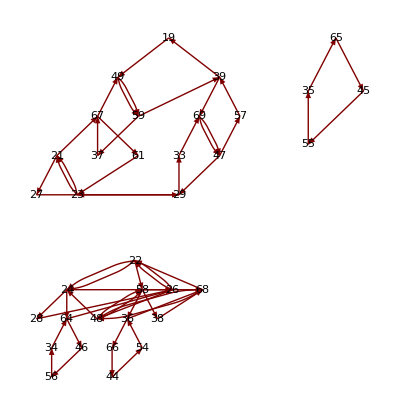

```mathematica
TreePlot[Sl2∪Sl3∪Tl2∪Tl4,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T5=Exch[{StartSet,StartSet/.S6/.S3/.S3/.IS6/.S3/.S6/.S3/.IS6}](*S6^-1 S3 S6 S3 S6^-1 S3^2 S6*)
T6=Exch[{StartSet,StartSet/.S4/.S5/.S6/.T4/.IS4/.IS5/.IS6}](*S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6*)
```

{21→39,22→26,23→27,24→22,26→24,27→69,29→47,37→23,39→59,47→67,48→68,49→37,57→49,58→48,59→29,67→21,68→58,69→57}

{28→34,34→36,36→28,38→54,54→64,64→38}

```mathematica
IT5=Exch[{StartSet,StartSet/.T5/.T5/.T5/.T5/.T5}];
```

```mathematica
IT6=Exch[{StartSet,StartSet/.T6/.T6}];
```

```mathematica
Table[{T6[[i]],"T6"},{i,Length[T6]}]//InputForm
```

{{28 -> 34, "T6"}, {34 -> 36, "T6"}, {36 -> 28, "T6"}, {38 -> 54, "T6"}, {54 -> 64, "T6"}, {64 -> 38, "T6"}}

```mathematica
Tl5={{21->39,"T5"},{22->26,"T5"},{23->27,"T5"},{24->22,"T5"},{26->24,"T5"},{27->69,"T5"},{29->47,"T5"},{37->23,"T5"},{39->59,"T5"},{47->67,"T5"},{48->68,"T5"},{49->37,"T5"},{57->49,"T5"},{58->48,"T5"},{59->29,"T5"},{67->21,"T5"},{68->58,"T5"},{69->57,"T5"}};
Tl6={{28->34,"T6"},{34->36,"T6"},{36->28,"T6"},{38->54,"T6"},{54->64,"T6"},{64->38,"T6"}};
```

```mathematica
S2,S3,T2=S7^-1 S3 S7,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32不动的完备系,19到任意位置*)

S2,S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T6=S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61不动的完备系,34到任意位置*)
```

```mathematica
TreePlot[Sl2∪Sl3∪Tl4∪Tl5∪Tl6,VertexLabeling->True,DirectedEdges-> True]
```

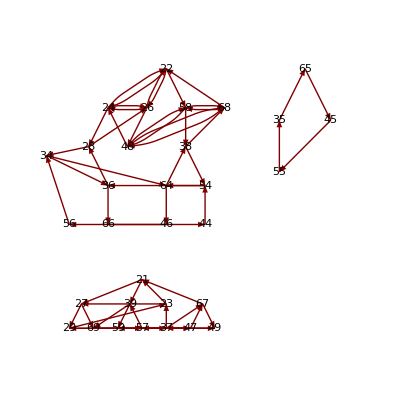

```mathematica
T7=Exch[{StartSet,StartSet/.IS1/.IS2/.IS3/.S4/.S5/.S6/.T4/.IS4/.IS5/.IS6/.S1/.S2/.S3}](*S1 S2 S3 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^-1 S2^-1 S3^-1*)
T8=Exch[{StartSet,StartSet/.S1/.S1/.S2/.S2/.S3/.S3/.S4/.S5/.S6/.T4/.IS4/.IS5/.IS6/.S1/.S1/.S2/.S2/.S3/.S3}](*S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2*)
```

{26→64,36→46,46→68,64→66,66→26,68→36}

{22→46,44→22,46→44,48→66,56→48,66→56}

```mathematica
IT7=Exch[{StartSet,StartSet/.T7/.T7}];
```

```mathematica
IT8=Exch[{StartSet,StartSet/.T8/.T8}];
```

```mathematica
Table[{T8[[i]],"T8"},{i,Length[T8]}]//InputForm
```

{{22 -> 46, "T8"}, {44 -> 22, "T8"}, {46 -> 44, "T8"}, {48 -> 66, "T8"}, {56 -> 48, "T8"}, {66 -> 56, "T8"}}

```mathematica
Tl7={{26->64,"T7"},{36->46,"T7"},{46->68,"T7"},{64->66,"T7"},{66->26,"T7"},{68->36,"T7"}};
Tl8={{22->46,"T8"},{44->22,"T8"},{46->44,"T8"},{48->66,"T8"},{56->48,"T8"},{66->56,"T8"}};
```

```mathematica
S2,S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T6=S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61不动的完备系,34到任意位置*)

S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T7=S1 S2 S3 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^-1 S2^-1 S3^-1,T8=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54不动的完备系,36到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl4∪Tl5∪Tl7∪Tl8,VertexLabeling->True,DirectedEdges-> True]
```

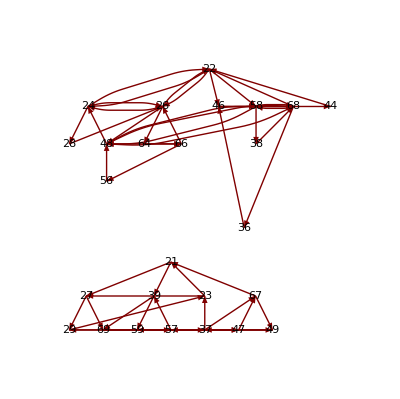

```mathematica
S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T7=S1 S2 S3 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^-1 S2^-1 S3^-1,T8=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54不动的完备系,36到任意位置*)

S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T8=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64不动的完备系,44到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl4∪Tl5∪Tl8,VertexLabeling->True,DirectedEdges-> True]
```

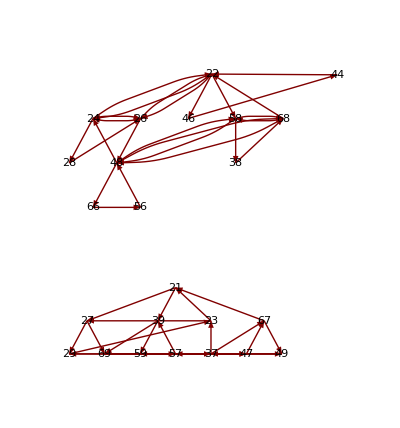

```mathematica
T9=Exch[{StartSet,StartSet/.T8/.T8/.S3/.T8}](*T8 S3 T8^-1=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2 S3 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3^-1 S5 S3^2 S5^-1 S3^-1 S5  S4 S5 S6 S1^2 S2^2 S3^2 *)
```

{21→27,23→21,24→28,26→46,27→29,28→26,29→23,37→67,38→68,39→69,46→24,47→57,49→59,57→39,58→38,59→37,66→58,67→49,68→66,69→47}

```mathematica
IT9=Exch[{StartSet,StartSet/.T9/.T9/.T9}];
```

```mathematica
Table[{T9[[i]],"T9"},{i,Length[T9]}]//InputForm
```

{{21 -> 27, "T9"}, {23 -> 21, "T9"}, {24 -> 28, "T9"}, {26 -> 46, "T9"}, {27 -> 29, "T9"}, {28 -> 26, "T9"}, {29 -> 23, "T9"}, {37 -> 67, "T9"}, 
 {38 -> 68, "T9"}, {39 -> 69, "T9"}, {46 -> 24, "T9"}, {47 -> 57, "T9"}, {49 -> 59, "T9"}, {57 -> 39, "T9"}, {58 -> 38, "T9"}, {59 -> 37, "T9"}, 
 {66 -> 58, "T9"}, {67 -> 49, "T9"}, {68 -> 66, "T9"}, {69 -> 47, "T9"}}

```mathematica
Tl9={{21->27,"T9"},{23->21,"T9"},{24->28,"T9"},{26->46,"T9"},{27->29,"T9"},{28->26,"T9"},{29->23,"T9"},{37->67,"T9"},{38->68,"T9"},{39->69,"T9"},{46->24,"T9"},{47->57,"T9"},{49->59,"T9"},{57->39,"T9"},{58->38,"T9"},{59->37,"T9"},{66->58,"T9"},{67->49,"T9"},{68->66,"T9"},{69->47,"T9"}};
```

```mathematica
S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T8=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64不动的完备系,44到任意位置*)

S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T9=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2 S3 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3^-1 S5 S3^2 S5^-1 S3^-1 S5  S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56不动的完备系,46到任意位置*)
```

```mathematica
TreePlot[Sl3∪Tl4∪Tl5∪Tl9,VertexLabeling->True,DirectedEdges-> True]
```

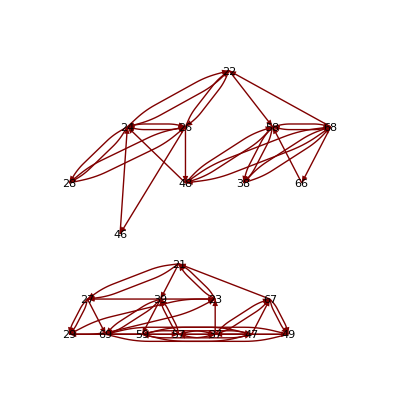

```mathematica
T10=Exch[{StartSet,StartSet/.S6/.S9/.IS3/.IS9/.S3/.IS6}](*S6^-1 S3 S9^-1 S3^-1 S9 S6*)
T11=Exch[{StartSet,StartSet/.S6/.S3/.S3/.IS6/.S3/.S6/.IS3/.IS6/.S3/.S6/.S3/.IS6}](*S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6*)
T12=Exch[{StartSet,StartSet/.S6/.S3/.T4/.T10/.IS6}](*S6^-1 T10 T4 S3 S6=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6*)
```

{21→27,22→24,23→29,24→68,26→48,27→47,29→49,37→21,39→23,47→57,48→58,49→67,57→59,58→26,59→37,67→69,68→22,69→39}

{21→59,22→24,23→69,24→26,26→22,27→57,29→67,37→27,39→29,47→21,48→58,49→23,57→37,58→68,59→47,67→39,68→48,69→49}

{21→47,22→48,24→28,27→29,28→58,29→37,37→67,38→24,39→27,47→59,48→22,57→39,58→38,59→21,67→57}

```mathematica
Table[{T12[[i]],"T12"},{i,Length[T12]}]//InputForm
```

{{21 -> 47, "T12"}, {22 -> 48, "T12"}, {24 -> 28, "T12"}, {27 -> 29, "T12"}, {28 -> 58, "T12"}, {29 -> 37, "T12"}, {37 -> 67, "T12"}, 
 {38 -> 24, "T12"}, {39 -> 27, "T12"}, {47 -> 59, "T12"}, {48 -> 22, "T12"}, {57 -> 39, "T12"}, {58 -> 38, "T12"}, {59 -> 21, "T12"}, 
 {67 -> 57, "T12"}}

```mathematica
Tl10={{21->27,"T10"},{22->24,"T10"},{23->29,"T10"},{24->68,"T10"},{26->48,"T10"},{27->47,"T10"},{29->49,"T10"},{37->21,"T10"},{39->23,"T10"},{47->57,"T10"},{48->58,"T10"},{49->67,"T10"},{57->59,"T10"},{58->26,"T10"},{59->37,"T10"},{67->69,"T10"},{68->22,"T10"},{69->39,"T10"}};
Tl11={{21->59,"T11"},{22->24,"T11"},{23->69,"T11"},{24->26,"T11"},{26->22,"T11"},{27->57,"T11"},{29->67,"T11"},{37->27,"T11"},{39->29,"T11"},{47->21,"T11"},{48->58,"T11"},{49->23,"T11"},{57->37,"T11"},{58->68,"T11"},{59->47,"T11"},{67->39,"T11"},{68->48,"T11"},{69->49,"T11"}};
Tl12={{21->47,"T12"},{22->48,"T12"},{24->28,"T12"},{27->29,"T12"},{28->58,"T12"},{29->37,"T12"},{37->67,"T12"},{38->24,"T12"},{39->27,"T12"},{47->59,"T12"},{48->22,"T12"},{57->39,"T12"},{58->38,"T12"},{59->21,"T12"},{67->57,"T12"}};
```

```mathematica
S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T9=S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S4 S5 S6 S1^2 S2^2 S3^2 S3 S1^2 S2^2 S3^2 S4^-1 S5^-1 S6^-1 S5^-1 S3^-1 S5 S3^2 S5^-1 S3^-1 S5  S4 S5 S6 S1^2 S2^2 S3^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56不动的完备系,46到任意位置*)

S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T11=S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6,T12=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66不动的完备系,21到任意位置*)
```

```mathematica
T10^6=e;T11^3=e;T12^12=e;T5^6=e;
```

```mathematica
IT10=Exch[{StartSet,StartSet/.T10/.T10/.T10/.T10/.T10}];
IT11=Exch[{StartSet,StartSet/.T11/.T11}];
IT12=Exch[{StartSet,StartSet/.T12/.T12/.T12/.T12/.T12/.T12/.T12/.T12/.T12/.T12/.T12}];
IT5=Exch[{StartSet,StartSet/.T5/.T5/.T5/.T5/.T5}];
```

```mathematica
TreePlot[Sl3∪Tl4∪Tl5∪Tl10∪Tl11∪Tl12,VertexLabeling->True,DirectedEdges-> True]
```

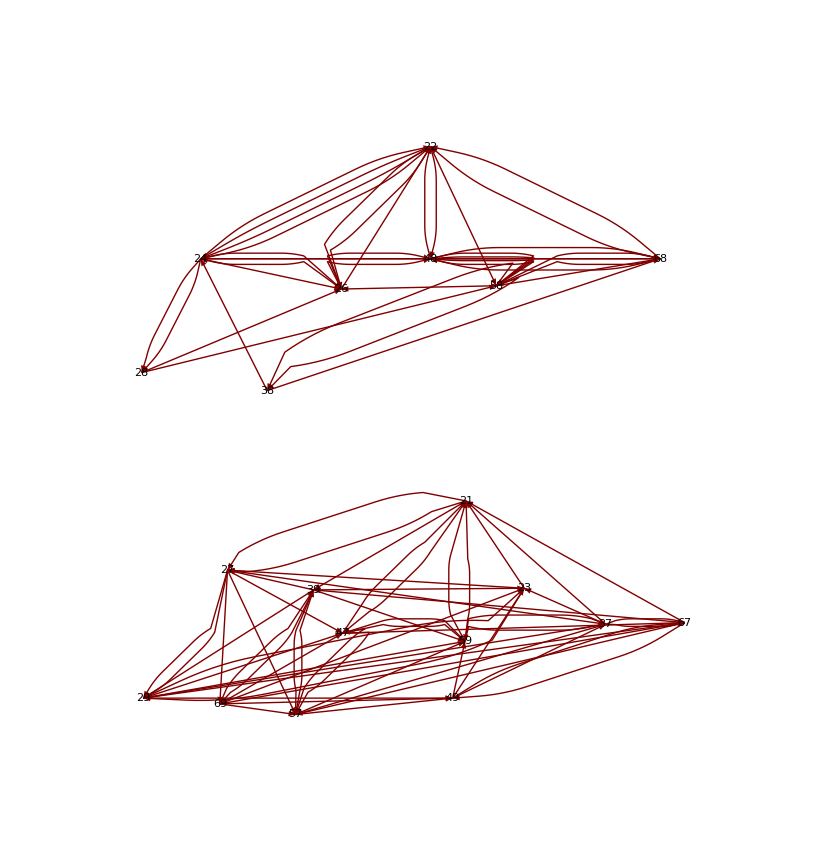

```mathematica
Exch[{StartSet,StartSet/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3}]
```

{24→58,28→38,38→28,58→24}

```mathematica
Exch[{StartSet,StartSet/.T5/.T12/.IS3}]
```

{22→28,23→27,24→68,26→24,27→39,28→48,29→49,37→29,38→22,39→23,48→38,49→37,57→67,58→26,67→69,68→58,69→57}

```mathematica
T13=Exch[{StartSet,StartSet/.T12/.T11}](*T11 T12=S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6 S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6*)
T14=Exch[{StartSet,StartSet/.T10/.IS3}](*S3^-1 T10=S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6*)
T15=Exch[{StartSet,StartSet/.S3/.S3/.T14/.T5}](*T5 T14 S3^2=S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S3^2*)
T16=Exch[{StartSet,StartSet/.T5/.T5/.T12}](*T12 T5^2=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6*)
```

{22→58,23→69,24→28,26→22,27→67,28→68,29→27,37→39,38→26,39→57,48→24,49→23,57→29,58→38,67→37,68→48,69→49}

{23→27,24→38,26→68,27→69,28→24,29→67,37→23,38→58,39→29,49→37,57→49,58→28,67→39,68→26,69→57}

{23→57,24→58,26→38,27→69,28→26,29→39,37→23,38→68,39→67,49→27,57→49,58→24,67→29,68→28,69→37}

{22→28,23→69,24→26,26→48,27→39,28→58,29→57,37→29,38→24,39→37,48→38,49→23,57→67,58→68,67→27,68→22,69→49}

```mathematica
IT13=Exch[{StartSet,StartSet/.T13/.T13/.T13/.T13/.T13/.T13/.T13/.T13/.T13/.T13/.T13}];
```

```mathematica
IT14=Exch[{StartSet,StartSet/.T14/.T14/.T14/.T14/.T14/.T14/.T14/.T14/.T14/.T14/.T14}];
```

```mathematica
IT15=Exch[{StartSet,StartSet/.T15/.T15/.T15/.T15/.T15/.T15/.T15/.T15/.T15/.T15/.T15}];
```

```mathematica
IT16=Exch[{StartSet,StartSet/.T16/.T16/.T16/.T16/.T16/.T16/.T16/.T16/.T16/.T16/.T16}];
```

```mathematica
Table[{T16[[i]],"T16"},{i,Length[T16]}]//InputForm
```

{{22 -> 28, "T16"}, {23 -> 69, "T16"}, {24 -> 26, "T16"}, {26 -> 48, "T16"}, {27 -> 39, "T16"}, {28 -> 58, "T16"}, {29 -> 57, "T16"}, 
 {37 -> 29, "T16"}, {38 -> 24, "T16"}, {39 -> 37, "T16"}, {48 -> 38, "T16"}, {49 -> 23, "T16"}, {57 -> 67, "T16"}, {58 -> 68, "T16"}, 
 {67 -> 27, "T16"}, {68 -> 22, "T16"}, {69 -> 49, "T16"}}

```mathematica
Tl13={{22->58,"T13"},{23->69,"T13"},{24->28,"T13"},{26->22,"T13"},{27->67,"T13"},{28->68,"T13"},{29->27,"T13"},{37->39,"T13"},{38->26,"T13"},{39->57,"T13"},{48->24,"T13"},{49->23,"T13"},{57->29,"T13"},{58->38,"T13"},{67->37,"T13"},{68->48,"T13"},{69->49,"T13"}};
Tl14={{23->27,"T14"},{24->38,"T14"},{26->68,"T14"},{27->69,"T14"},{28->24,"T14"},{29->67,"T14"},{37->23,"T14"},{38->58,"T14"},{39->29,"T14"},{49->37,"T14"},{57->49,"T14"},{58->28,"T14"},{67->39,"T14"},{68->26,"T14"},{69->57,"T14"}};
Tl15={{23->57,"T15"},{24->58,"T15"},{26->38,"T15"},{27->69,"T15"},{28->26,"T15"},{29->39,"T15"},{37->23,"T15"},{38->68,"T15"},{39->67,"T15"},{49->27,"T15"},{57->49,"T15"},{58->24,"T15"},{67->29,"T15"},{68->28,"T15"},{69->37,"T15"}};
Tl16={{22->28,"T16"},{23->69,"T16"},{24->26,"T16"},{26->48,"T16"},{27->39,"T16"},{28->58,"T16"},{29->57,"T16"},{37->29,"T16"},{38->24,"T16"},{39->37,"T16"},{48->38,"T16"},{49->23,"T16"},{57->67,"T16"},{58->68,"T16"},{67->27,"T16"},{68->22,"T16"},{69->49,"T16"}};
```

```mathematica
S3,T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T5=S6^-1 S3 S6 S3 S6^-1 S3^2 S6,T10=S6^-1 S3 S9^-1 S3^-1 S9 S6,T11=S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6,T12=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66不动的完备系,21到任意位置*)

T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T13=T11 T12=S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6 S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6,T14=S3^-1 T10=S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6,T15=T5 T14 S3^2=S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S3^2,T16=T12 T5^2=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6=
S6^2 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3^2 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59不动的完备系,23到任意位置*)
```

```mathematica
TreePlot[Tl4∪Tl13∪Tl14∪Tl15∪Tl16,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
IT13=Exch[{StartSet,StartSet/.IT11/.IT12}];
IT14=Exch[{StartSet,StartSet/.S3/.IT10}];
IT15=Exch[{StartSet,StartSet/.IT5/.IT14/.S3/.S3}];
IT16=Exch[{StartSet,StartSet/.IT12/.IT5/.IT5}];
```

```mathematica
T17=Exch[{StartSet,StartSet/.T16/.IT13}](*T13^-1 T16=T12^-1 T11^-1 T12 T5^2*)
T18=Exch[{StartSet,StartSet/.IT15/.T14}](*T14 T15^-1=S3^-1 T10 S3^2 T14^-1 T5^-1*)
T19=Exch[{StartSet,StartSet/.T14/.T14/.IT13}](*T13^-1 T14^2=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10*)
```

{22→24,24→38,26→68,27→37,28→22,29→39,37→57,38→48,39→67,48→58,57→27,58→28,67→29,68→26}

{24→28,26→24,27→37,28→26,29→39,37→57,38→68,39→67,57→27,58→38,67→29,68→58}

{22→26,24→22,26→38,27→39,28→58,29→37,37→29,38→24,39→27,48→68,57→67,58→48,67→57,68→28}

```mathematica
IT17=Exch[{StartSet,StartSet/.T17/.T17/.T17/.T17/.T17}];
```

```mathematica
IT18=Exch[{StartSet,StartSet/.T18/.T18}];
```

```mathematica
IT19=Exch[{StartSet,StartSet/.T19/.T19/.T19}];
```

```mathematica
Table[{T19[[i]],"T19"},{i,Length[T19]}]//InputForm
```

{{22 -> 26, "T19"}, {24 -> 22, "T19"}, {26 -> 38, "T19"}, {27 -> 39, "T19"}, {28 -> 58, "T19"}, {29 -> 37, "T19"}, {37 -> 29, "T19"}, 
 {38 -> 24, "T19"}, {39 -> 27, "T19"}, {48 -> 68, "T19"}, {57 -> 67, "T19"}, {58 -> 48, "T19"}, {67 -> 57, "T19"}, {68 -> 28, "T19"}}

```mathematica
Tl17={{22->24,"T17"},{24->38,"T17"},{26->68,"T17"},{27->37,"T17"},{28->22,"T17"},{29->39,"T17"},{37->57,"T17"},{38->48,"T17"},{39->67,"T17"},{48->58,"T17"},{57->27,"T17"},{58->28,"T17"},{67->29,"T17"},{68->26,"T17"}};
Tl18={{24->28,"T18"},{26->24,"T18"},{27->37,"T18"},{28->26,"T18"},{29->39,"T18"},{37->57,"T18"},{38->68,"T18"},{39->67,"T18"},{57->27,"T18"},{58->38,"T18"},{67->29,"T18"},{68->58,"T18"}};
Tl19={{22->26,"T19"},{24->22,"T19"},{26->38,"T19"},{27->39,"T19"},{28->58,"T19"},{29->37,"T19"},{37->29,"T19"},{38->24,"T19"},{39->27,"T19"},{48->68,"T19"},{57->67,"T19"},{58->48,"T19"},{67->57,"T19"},{68->28,"T19"}};
```

```mathematica
T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T13=T11 T12=S6^-1 S3 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6 S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6,T14=S3^-1 T10=S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6,T15=T5 T14 S3^2=S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S3^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S3^2,T16=T12 T5^2=S6^-1 S6^-1 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6 S6^-1 S3 S6 S3 S6^-1 S3^2 S6=
S6^2 S3 S9^-1 S3^-1 S9 S6 S5^-1 S3 S5 S3^2 S5^-1 S3 S5 S3^2 S6 S3 S6^-1 S3^-1 S6 S3 S6^-1 S3^2 S6
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59不动的完备系,23到任意位置*)

T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T17=T12^-1 T11^-1 T12 T5^2,T18=S3^-1 T10 S3^2 T14^-1 T5^-1,T19=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69不动的完备系,27到任意位置*)
```

```mathematica
TreePlot[Tl4∪Tl17∪Tl18∪Tl19,VertexLabeling->True,DirectedEdges-> True]
```

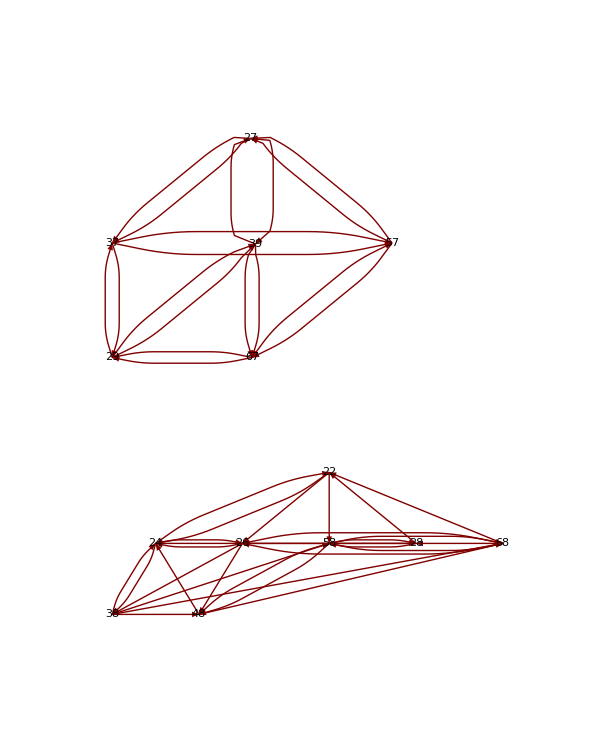

```mathematica
T20=Exch[{StartSet,StartSet/.T19/.T19}](*T19^2=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10 T12^-1 T11^-1 S3^-1 T10 S3^-1 T10*)
T21=Exch[{StartSet,StartSet/.T17/.T17/.T17}](*T17^3=T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2*)
```

{22→38,24→26,26→24,28→48,38→22,48→28,58→68,68→58}

{22→48,24→58,26→68,28→38,38→28,48→22,58→24,68→26}

```mathematica
IT20=Exch[{StartSet,StartSet/.T20}];
```

```mathematica
IT21=Exch[{StartSet,StartSet/.T21}];
```

```mathematica
Table[{T21[[i]],"T21"},{i,Length[T21]}]//InputForm
```

{{22 -> 48, "T21"}, {24 -> 58, "T21"}, {26 -> 68, "T21"}, {28 -> 38, "T21"}, {38 -> 28, "T21"}, {48 -> 22, "T21"}, {58 -> 24, "T21"}, 
 {68 -> 26, "T21"}}

```mathematica
Tl20={{22->38,"T20"},{24->26,"T20"},{26->24,"T20"},{28->48,"T20"},{38->22,"T20"},{48->28,"T20"},{58->68,"T20"},{68->58,"T20"}};
Tl21={{22->48,"T21"},{24->58,"T21"},{26->68,"T21"},{28->38,"T21"},{38->28,"T21"},{48->22,"T21"},{58->24,"T21"},{68->26,"T21"}};
```

```mathematica
T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T17=T12^-1 T11^-1 T12 T5^2,T18=S3^-1 T10 S3^2 T14^-1 T5^-1,T19=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69不动的完备系,27到任意位置*)

T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T20=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10 T12^-1 T11^-1 S3^-1 T10 S3^-1 T10,T21=T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47不动的完备系,27到任意位置*)
```

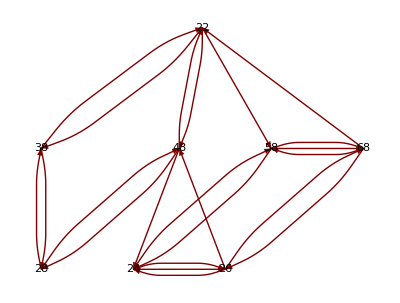

```mathematica
TreePlot[Tl4∪Tl20∪Tl21,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
Exch[{StartSet,StartSet/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3/.T10/.IS3}]
```

{24→58,28→38,38→28,58→24}

```mathematica
T22=Exch[{StartSet,StartSet/.S1/.S1/.S2/.S2/.S3/.S3/.T4/.S1/.S1/.S2/.S2/.S3/.S3}](*S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2*)
T23=Exch[{StartSet,StartSet/.T4/.T20/.T4/.T22}](*S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2 T4 T20 T4*)
```

{24→38,26→24,28→68,38→26,58→28,68→58}

{26→68,28→38,38→28,68→26}

```mathematica
IT22=Exch[{StartSet,StartSet/.T22/.T22}];
```

```mathematica
IT23=Exch[{StartSet,StartSet/.T23}];
```

```mathematica
Table[{T23[[i]],"T23"},{i,Length[T23]}]//InputForm
```

{{26 -> 68, "T23"}, {28 -> 38, "T23"}, {38 -> 28, "T23"}, {68 -> 26, "T23"}}

```mathematica
Tl22={{24->38,"T22"},{26->24,"T22"},{28->68,"T22"},{38->26,"T22"},{58->28,"T22"},{68->58,"T22"}};
Tl23={{26->68,"T23"},{28->38,"T23"},{38->28,"T23"},{68->26,"T23"}};
```

```mathematica
T4=S5^-1 S3 S5 S3^2 S5^-1 S3 S5,T20=T12^-1 T11^-1 S3^-1 T10 S3^-1 T10 T12^-1 T11^-1 S3^-1 T10 S3^-1 T10,T21=T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2 T12^-1 T11^-1 T12 T5^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47不动的完备系,27到任意位置*)

T22=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2,T23=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2 T4 T20 T4
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48不动的完备系,24到任意位置*)
```

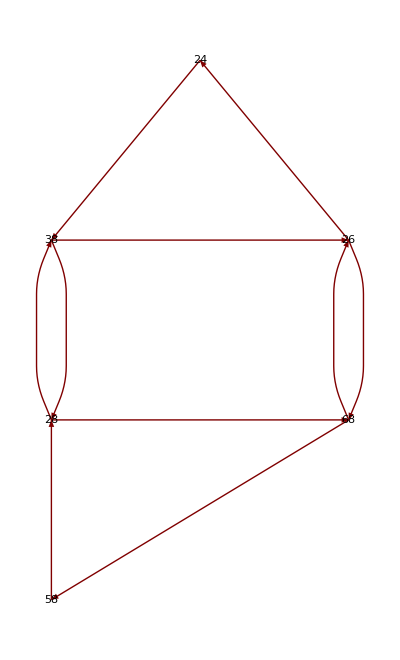

```mathematica
TreePlot[Tl22∪Tl23,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T24=Exch[{StartSet,StartSet/.IS5/.T20/.S5/.S5/.T3/.S3/.T3/.T3/.T21}](*T21 T3^2 S3 T3 S5^2 T20 S5^-1*);
IT24=Exch[{StartSet,StartSet/.T24/.T24/.T24}];
```

```mathematica
Tl24={{15->35,"T24"},{25->45,"T24"},{26->28,"T24"},{28->26,"T24"},{35->25,"T24"},{38->68,"T24"},{45->15,"T24"},{68->38,"T24"}};
```

```mathematica
T22=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2,T23=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2 T4 T20 T4
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48不动的完备系,24到任意位置*)

T23=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2 T4 T20 T4,T24=T21 T3^2 S3 T3 S5^2 T20 S5^-1
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48,24,58不动的完备系,26到任意位置*)
```

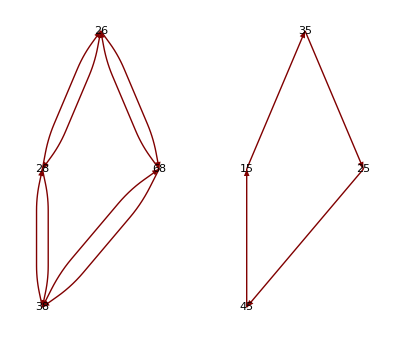

```mathematica
TreePlot[Tl23∪Tl24,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T25=Exch[{StartSet,StartSet/.S5/.S5/.S2/.S5/.S5/.IS2}](*S2^-1 S5^2 S2 S5^2*)
T26=Exch[{StartSet,StartSet/.S2/.S2/.S5/.S2/.S2/.IS5}](*S5^-1 S2^2 S5 S2^2*)
```

{35→45,45→35,55→65,65→55}

{15→25,25→15,35→45,45→35}

```mathematica
IT25=Exch[{StartSet,StartSet/.T25}];
IT26=Exch[{StartSet,StartSet/.T26}];
```

```mathematica
Table[{T27[[i]],"T27"},{i,Length[T27]}]//InputForm
```

{{15 -> 65, "T27"}, {25 -> 55, "T27"}, {35 -> 15, "T27"}, {45 -> 25, "T27"}, {55 -> 45, "T27"}, {65 -> 35, "T27"}}

```mathematica
Tl25={{35->45,"T25"},{45->35,"T25"},{55->65,"T25"},{65->55,"T25"}};
Tl26={{15->25,"T26"},{25->15,"T26"},{35->45,"T26"},{45->35,"T26"}};
Tl27={{15->65,"T27"},{25->55,"T27"},{35->15,"T27"},{45->25,"T27"},{55->45,"T27"},{65->35,"T27"}};
```

```mathematica
T23=S1^2 S2^2 S3^2 T4 S1^2 S2^2 S3^2 T4 T20 T4,T24=T21 T3^2 S3 T3 S5^2 T20 S5^-1
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48,24,58不动的完备系,26到任意位置*)

T25=S2^-1 S5^2 S2 S5^2,T26=S5^-1 S2^2 S5 S2^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48,24,58,26,68,28,38不动的完备系,15到任意位置*)
```

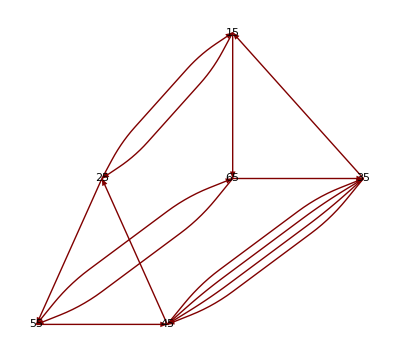

```mathematica
TreePlot[Tl25∪Tl26∪Tl27,VertexLabeling->True,DirectedEdges-> True]
```

```mathematica
T25=S2^-1 S5^2 S2 S5^2,T26=S5^-1 S2^2 S5 S2^2,T27=S5^-1 S2 S5 S1 S2^-1 S1^-1
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48,24,58,26,68,28,38不动的完备系,15到任意位置*)

T25=S2^-1 S5^2 S2 S5^2
(*保持11,41,53,12,42,13,63,43,14,54,16,62,17,31,51,18,32,19,33,61,34,54,36,64,44,56,46,66,21,47,59,23,49,69,27,37,57,29,39,47,22,48,24,58,26,68,28,38,15,25不动的完备系,35到任意位置*)
```